## Random XX chain: entanglement entropy

```mathematica
L=64;
ll=16;
shift=24;
(*nsample=5;
data={};
Monitor[For[n=1,n≤nsample,n++,
*)JJ=Table[RandomReal[],{i,1,L-1}];
JJ={0.0569831,0.929319,0.857543,0.481051,0.801281,0.425303,0.703691,0.218375,0.826938,0.0586994,0.10598,0.331061,0.999297,0.696844,0.459171,0.0839291,0.405155,0.593447,0.306421,0.965515,0.289701,0.299718,0.632453,0.20751,0.659349,0.062487,0.98814,0.161101,0.796633,0.589531,0.089963,0.0224802,0.629168,0.31329,0.38412,0.126697,0.30479,0.291914,0.251891,0.406708,0.565424,0.250488,0.506655,0.299114,0.233593,0.481964,0.471047,0.434223,0.210708,0.244366,0.405669,0.78991,0.128383,0.633564,0.687497,0.0107988,0.000134108,0.950426,0.520097,0.9801,0.302213,0.960798,0.18187};

AppendTo[JJ,0];T=Table[(KroneckerDelta[i,j-1] JJ⟦j-1⟧)/2.+(KroneckerDelta[i,j+1] JJ⟦j⟧)/2.,{i,1,L},{j,1,L}];Spect=Eigensystem[T];ind=Table[i,{i,1,L}];eigval=Spect⟦1⟧;ind=Select[ind,eigval⟦#1⟧<0&];eigvec=Table[Spect⟦2,ind⟦k⟧⟧,{k,1,Length[ind]}];Corr[x_,y_]:=Total[Table[eigvec⟦q,x⟧ eigvec⟦q,y⟧,{q,1,Length[eigvec]}]];ent={};For[k=1,k≤L/4,k++,shift=1/2 (L-2 k);ll=2 k;cmat=Table[Corr[shift+x,shift+y],{x,1,ll},{y,1,ll}];eeig=Eigenvalues[cmat];Ent=∑_(i=1)^Length[eeig] If[Abs[eeig⟦i⟧]>0&&Abs[eeig⟦i⟧]<1,(1-eeig⟦i⟧) (-Log[1-eeig⟦i⟧])-eeig⟦i⟧ Log[eeig⟦i⟧],0];AppendTo[ent,{2k,Ent}];];
ent
(*AppendTo[data,ent];];,{n}]*)
```

{{2,1.38486},{4,0.803286},{6,1.39581},{8,0.180068},{10,1.4002},{12,0.545538},{14,1.42621},{16,0.703124},{18,1.55082},{20,0.786137+1.1792×10^-15 ⅈ},{22,1.57491+8.73074×10^-16 ⅈ},{24,1.82253+6.68901×10^-16 ⅈ},{26,1.53119+2.86086×10^-15 ⅈ},{28,2.06321+1.29306×10^-15 ⅈ},{30,1.74258+3.84548×10^-15 ⅈ},{32,1.32907+2.54086×10^-15 ⅈ}}

```mathematica
ex=Import["/u/he/valba/Github/negatitivy/ran_negativity/mathematica/re"] ;
```

```mathematica
ex[[3]]
```

{{1.383628902159025,1.81055,1.43248,1.39516,1.62983,1.42628,2.1353, 1.9119885950487108 + 1.2599858674912698*^-15*I,1.57245,2.06775, 1.7872774326297372 + 1.0931349472878151*^-15*I, 1.8953178403155464 + 6.270384076621184*^-16*I, 1.5083824124404257 + 1.0328330607015858*^-15*I, 2.3908333110367845 + 2.2602515226747766*^-15*I, 1.6209414088484106 + 8.380312721548843*^-16*I, 2.0796521755145303 + 3.3801724110061083*^-15*I, 2.3465777886053774 + 6.294449863093254*^-15*I, 2.0830824875998535 + 3.4699650337039792*^-15*I, 2.6915301511084624 + 4.385245803933934*^-15*I, 1.4907855842373379 + 6.094734018503764*^-15*I, 2.744899475597132 + 5.591985963694587*^-15*I, 2.3544245124874816 + 4.2675088586950095*^-15*I, 2.9118718558914036 + 4.263126614193246*^-15*I, 2.8706538777475843 + 4.431545177104931*^-15*I, 2.914714925111556 + 6.7334731402088055*^-15*I, 2.4456069508659812 + 7.487711922975561*^-15*I, 2.0425310810482507 + 6.087491532021622*^-15*I, 2.2290157939759454 + 7.079765827709471*^-15*I, 2.550930015304841 + 8.25982165869359*^-15*I, 2.205144265321108 + 5.996650565533444*^-15*I, 1.4079009468506314 + 1.1378284051590499*^-14*I, 2.4447667325285 + 9.100254901487923*^-15*I}}

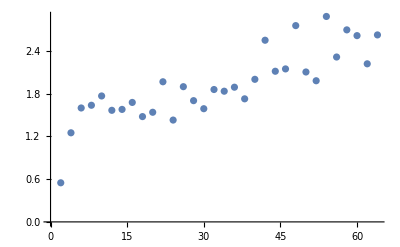

```mathematica
ent//ListPlot
```

```mathematica
ent
```

{{2,0.549197},{4,1.2513},{6,1.59974},{8,1.63797},{10,1.76846},{12,1.56693},{14,1.57969},{16,1.67755},{18,1.47877},{20,1.53949},{22,1.96779+6.93887×10^-16 ⅈ},{24,1.43007+3.0532×10^-16 ⅈ},{26,1.89883+1.76473×10^-15 ⅈ},{28,1.70262+3.70292×10^-15 ⅈ},{30,1.58956+2.94852×10^-15 ⅈ},{32,1.859+1.1251×10^-15 ⅈ},{34,1.83529+3.04921×10^-15 ⅈ},{36,1.89153+3.09974×10^-15 ⅈ},{38,1.7282+5.99742×10^-15 ⅈ},{40,2.00217+3.6951×10^-15 ⅈ},{42,2.55108+6.01912×10^-15 ⅈ},{44,2.11548+3.70571×10^-15 ⅈ},{46,2.14833+6.21078×10^-15 ⅈ},{48,2.75643+6.18738×10^-15 ⅈ},{50,2.10517+6.22201×10^-15 ⅈ},{52,1.98216+3.24065×10^-15 ⅈ},{54,2.88492+5.4855×10^-15 ⅈ},{56,2.31538+3.86223×10^-15 ⅈ},{58,2.69656+7.38981×10^-15 ⅈ},{60,2.61572+1.27296×10^-14 ⅈ},{62,2.21999+8.3174×10^-15 ⅈ},{64,2.62577+9.82154×10^-15 ⅈ}}

```mathematica
ent
```

{{2,0.91255},{4,1.04517},{6,1.40666},{8,0.597607},{10,1.46908},{12,1.06032},{14,1.39919},{16,0.0831358+2.6159×10^-16 ⅈ}}